# DM DM -> h2 h2

```mathematica
Quit;
```

```mathematica
ClearAll["Global`*"];
$FeynArtsPath=SetDirectory["~/Work/FeynArts-3.9"]
<<FeynArts`
SetDirectory[$FeynArtsPath<>""]
$FormCalcPath=SetDirectory["~/Work/FormCalc-8.3"]
<<FormCalc`
SetDirectory[$FormCalcPath<>""]
```

/home/anferivera/Work/FeynArts-3.9

FeynArts 3.9 (8 Jul 2015)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

/home/anferivera/Work/FeynArts-3.9

/home/anferivera/Work/FormCalc-8.3

FormCalc 8.3

by Thomas Hahn

last revised 14 Nov 13

/home/anferivera/Work/FormCalc-8.3

## Load the model, choose the topology and the diagram

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /home/anferivera/Work/FeynArts-3.9/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/anferivera/Work/FeynArts-3.9/Models/SDdiracDMEWSB.mod

> 54 particles (incl. antiparticles) in 19 classes

> $CounterTerms are ON

> 112 vertices

classes model {SDdiracDMEWSB} initialized

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

in total: 6 Particles insertions

> Top. 1: 2 diagrams

> Top. 2: 2 diagrams

> Top. 3: 2 diagrams

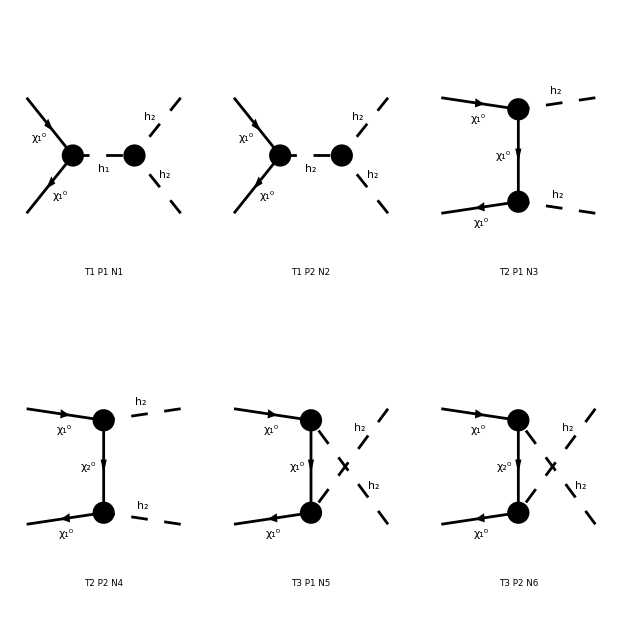

FeynArtsGraphics[{ComposedChar[\chi,1,0],ComposedChar[\chi,1,0]}→{ComposedChar[h,2],ComposedChar[h,2]}][([T1 P1 N1] | [T1 P2 N2] | [T2 P1 N3]
[T2 P2 N4] | [T3 P1 N5] | [T3 P2 N6])]

```mathematica
ClearProcess[];
n22=CreateTopologies[0,2->2]

d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{S[1,{2}],S[1,{2}]}, InsertionLevel->{Particles},Model->"SDdiracDMEWSB",GenericModel->"Lorentz"(*,ExcludeParticles->{S[1,{1}],F[6,{2}] }*) ];
(*d22=InsertFields[n22,{F[6,{1}],-F[6,{1}]}->{V[3],-V[3]}, InsertionLevel->{Particles},Model->"SDdiracDMvsEWSB",GenericModel->"Lorentz"];*)
Paint[d22,ColumnsXRows->{3,2}]
```

## Amplitude

```mathematica
amp=CreateFeynAmp[d22]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

in total: 6 Particles amplitudes

FeynAmpList[Process→{{F[6,{1}],p1,MassFxv[1],{}},{-F[6,{1}],p2,MassFxv[1],{}}}→{{S[1,{2}],k1,Masshh[2],{}},{S[1,{2}],k2,Masshh[2],{}}},Model→{SDdiracDMEWSB},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[1,1]+YRC XV[1,2]^* ZH[1,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[1,1]+YRC XV[1,2] ZH[1,2]))/(√2)).u[p1,MassFxv[1]] 1/((k1+k2)^2-Masshh[1]^2) (-ZH[2,2] (LSPH (vS ZH[1,1]+vvSM ZH[1,2]) ZH[2,1]+(LSPH vvSM ZH[1,1]+3 LSP vS ZH[1,2]) ZH[2,2])-ZH[2,1] ((3 Lam vvSM ZH[1,1]+LSPH vS ZH[1,2]) ZH[2,1]+LSPH (vS ZH[1,1]+vvSM ZH[1,2]) ZH[2,2]))],FeynAmp[GraphID[Topology==1,Generic==1,Particles==2,Number==2],Integral[],ⅈ v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((k1+k2)^2-Masshh[2]^2) (-ZH[2,2] (ZH[2,2] (LSPH vvSM ZH[2,1]+3 LSP vS ZH[2,2])+LSPH ZH[2,1] (vS ZH[2,1]+vvSM ZH[2,2]))-ZH[2,1] (ZH[2,1] (3 Lam vvSM ZH[2,1]+LSPH vS ZH[2,2])+LSPH ZH[2,2] (vS ZH[2,1]+vvSM ZH[2,2])))],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==3],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k2]+MassFxv[1]).(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k2)^2-MassFxv[1]^2)],FeynAmp[GraphID[Topology==2,Generic==1,Particles==2,Number==4],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[2,1]^* ZH[2,1]+YRC XV[2,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[2,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k2]+MassFxv[2]).(-(ⅈ XU[2,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[2,1] ZH[2,1]+YRC XV[2,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k2)^2-MassFxv[2]^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==5],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k1]+MassFxv[1]).(-(ⅈ XU[1,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k1)^2-MassFxv[1]^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==2,Number==6],Integral[],v̄[p2,MassFxv[1]].(-(ⅈ XU[1,2]^* om_- (YRD XV[2,1]^* ZH[2,1]+YRC XV[2,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[2,2] (YRD XV[1,1] ZH[2,1]+YRC XV[1,2] ZH[2,2]))/(√2)).(gs[-(p2)+k1]+MassFxv[2]).(-(ⅈ XU[2,2]^* om_- (YRD XV[1,1]^* ZH[2,1]+YRC XV[1,2]^* ZH[2,2]))/(√2)-(ⅈ om_+ XU[1,2] (YRD XV[2,1] ZH[2,1]+YRC XV[2,2] ZH[2,2]))/(√2)).u[p1,MassFxv[1]] 1/((p2-k1)^2-MassFxv[2]^2)]]

```mathematica
resultamp = CalcFeynAmp[amp,FermionChains->VA,FermionOrder->None,  Invariants->True]
```

preparing FORM code in /home/anferivera/Work/FormCalc-8.3/fc-amp-1.frm

running FORM...

ok

Amp[{{F[6,{1}],k[1],MassFxv[1],{}},{-F[6,{1}],k[2],MassFxv[1],{}}}→{{S[1,{2}],k[3],Masshh[2],{}},{S[1,{2}],k[4],Masshh[2],{}}}][(-(1/2 Sub32 Sub8 Den[S,Masshh[1]^2]+3/2 Sub11 Sub4 Den[S,Masshh[2]^2])/(√2)+1/4 (-Sub27 Den[T,MassFxv[2]^2]-Sub20 Den[U,MassFxv[2]^2]-Sub22 (Den[T,MassFxv[1]^2]+Den[U,MassFxv[1]^2]) MassFxv[1])) Mat[F1]+(-(1/2 Sub33 Sub8 Den[S,Masshh[1]^2]+3/2 Sub12 Sub4 Den[S,Masshh[2]^2])/(√2)+1/4 (-Sub30 (Den[T,MassFxv[2]^2]+Den[U,MassFxv[2]^2])-Sub14 (Den[T,MassFxv[1]^2]+Den[U,MassFxv[1]^2]) MassFxv[1])) Mat[F2]-Sub35 (1/4 Den[T,MassFxv[2]^2]-1/4 Den[U,MassFxv[2]^2]) Mat[F4]+Mat[F3] (Sub37 (1/4 Den[T,MassFxv[2]^2]-1/4 Den[U,MassFxv[2]^2])+Sub1 Sub10 XU[1,2]^* (1/2 Den[T,MassFxv[1]^2]-1/2 Den[U,MassFxv[1]^2]) XU[1,2])]

#### Rotation matrices in the singlet limit

```mathematica
Den[x_,y_]:=1/(x-y)
expr1=Simplify[Simplify[ComplexExpand[Plus@@resultamp//.Subexpr[]//.Abbr[]]/.Alfa->e^2/(4Pi)/.{MassFxv[1]->mx1,MassFxv[2]->mx2,Masshh[1]->mh1,Masshh[2]->mh2}/.{ZH[1,1]->Z11,ZH[1,2]->Z12,ZH[2,1]->-Z12,ZH[2,2]->Z11}/.{XV[1,1]->0,XV[1,2]->1,XV[2,1]->-1,XV[2,2]->0}/.{XU[1,1]->0,XU[1,2]->1,XU[2,1]->-1,XU[2,2]->0}/.YRD->0]/.(Z11^2+Z12^2)->1]
```

1/2 YRC ((2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))) Mat[<v2|1|u1>]-((T-U) YRC Z11^2 Mat[<v2|1,k[3]|u1>])/((mx1^2-T) (mx1^2-U)))

```mathematica
Simplify[expr1/.LSP->0/.LSPH->0]
```

1/2 YRC Z11 ((2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11+(3 √2 Lam (mh1^2-mh2^2) vvSM Z12^3)/((mh1^2-S) (-mh2^2+S))) Mat[<v2|1|u1>]+((-T+U) YRC Z11 Mat[<v2|1,k[3]|u1>])/((mx1^2-T) (mx1^2-U)))

#### Kine of Dirac Chains in the AMPLITUDE

```mathematica
InputForm[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->0,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->0}]
```

0

```mathematica
expr2 = Simplify[expr1/.{Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]->F1,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]->F5,
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]->F13,
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]->F53}]
```

1/2 YRC (-(F13 (T-U) YRC Z11^2)/((mx1^2-T) (mx1^2-U))+F1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))))

#### Factors in the AMPLITUDE

```mathematica
M1=Simplify[D[expr2,F1]]
```

1/2 YRC (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S)))

```mathematica
M2=Simplify[D[expr2,F5]]
```

0

```mathematica
M3=Simplify[D[expr2,F13]]
```

-((T-U) YRC^2 Z11^2)/(2 (mx1^2-T) (mx1^2-U))

```mathematica
M4=Simplify[D[expr2,F53]]
```

0

#### Factorization of the Amplitude

```mathematica
expr3 =(M1*F1+M2*F5+M3*F13+M4*F53);
```

```mathematica
Simplify[expr2 -expr3]
```

0

## Momenta in the computation for the CM frame

```mathematica
kinematic=Solve[{E1==Sqrt[p1^2+mx1^2]&&E2==Sqrt[p2^2+mh2^2]&& E2==E1},{E1,E2,p2}][[1]]
```

{E1→√(mx1^2+p1^2),E2→√(mx1^2+p1^2),p2→-√(-mh2^2+mx1^2+p1^2)}

In two dimensions...

```mathematica
k1={E1,p1,0,0};
k2={E1,-p1,0,0};
k3={E2,p2*ct,p2*st,0}/.st->Sqrt[1-ct^2];
k4={E2,-p2*ct,-p2*st,0}/.st->Sqrt[1-ct^2];
```

#### Mandelstan variables

```mathematica
guv = {{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}};
MatrixForm[guv]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
MV = Simplify[{S->(k1 + k2).guv.(k1 + k2),   
		         T->(k1 - k3).guv.(k1 - k3),   
                            U ->(k1 - k4).guv.(k1 - k4)}/.kinematic]
```

{S→4 (mx1^2+p1^2),T→mh2^2-mx1^2-2 p1 (p1+ct √(-mh2^2+mx1^2+p1^2)),U→mh2^2-mx1^2-2 p1 (p1-ct √(-mh2^2+mx1^2+p1^2))}

## Dirac spinors and Gamma matrices

Dirac matrices

```mathematica
gamma0={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
gamma1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
gamma2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
gamma3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};

gamma5={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
gammamu={gamma0,gamma1,gamma2,gamma3,gamma5};
```

```mathematica
Grid[{{"γ0","γ1","γ2","γ3","γ5"},{gamma0//MatrixForm,gamma1//MatrixForm,gamma2//MatrixForm,gamma3//MatrixForm,gamma5//MatrixForm}},Frame->All]
```

γ0 | γ1 | γ2 | γ3 | γ5
(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1) | (0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0) | (0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | ⅈ | 0 | 0
-ⅈ | 0 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0) | (0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Check properties of gamma matrices ...

```mathematica
Dot[gamma0,gamma0]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

[γu,γv]=2guv

```mathematica
Grid[{{"i=0","i=1","i=2","i=3"},{ Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma0}},{j,{gamma0}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma1}},{j,{gamma1}}]]//MatrixForm,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma2}},{j,{gamma2}}]] //MatrixForm ,Simplify[Sum[(Dot[i,j]+Dot[j,i]),{i,{gamma3}},{j,{gamma3}}]]//MatrixForm} },Frame->All]
```

i=0 | i=1 | i=2 | i=3
(2 | 0 | 0 | 0
0 | 2 | 0 | 0
0 | 0 | 2 | 0
0 | 0 | 0 | 2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2) | (-2 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 | 0
0 | 0 | 0 | -2)

```mathematica
χ[s_]:=If[s==1,{1,0},{0,1}]
Grid[{{χ1,χ2},{χ[1]//MatrixForm,χ[-1]//MatrixForm}},Frame->All]
```

χ1 | χ2
(1
0) | (0
1)

Spinors (Cheng appendix)

```mathematica
σp1=((Total[k1[[#+1]] PauliMatrix[#]&/@Range[3]])/(k1[[1]]+mx1));
σp2=((Total[k2[[#+1]] PauliMatrix[#]&/@Range[3]])/(k2[[1]]+mx1));
σp3=((Total[k3[[#+1]] PauliMatrix[#]&/@Range[3]])/(k3[[1]]+mx1));
σp4=((Total[k4[[#+1]] PauliMatrix[#]&/@Range[3]])/(k4[[1]]+mx1));
```

```mathematica
uspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{χ[s],Dot[eif,χ[s]]},1]
uspinor[1,σp2,mx1,k2[[1]]]
```

{√(E1+mx1),0,0,-p1/(√(E1+mx1))}

```mathematica
vspinor[s_,eif_,mif_,ki_]:=Sqrt[ki+mif] ArrayFlatten[{Dot[eif,χ[s]],χ[s]},1]
vspinor[1,σp2,mx1,k2[[1]]]
```

{0,-p1/(√(E1+mx1)),√(E1+mx1),0}

Check normalization for the U Spinors (input and output)

```mathematica
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.uspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[uspinor[1,σp2,mx1,k2[[1]]]]).gamma0.uspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.uspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[uspinor[1,σp4,mx1,k4[[1]]]]).gamma0.uspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

2 mx1

Check normalization for the V Spinors

```mathematica
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.vspinor[1,σp1,mx1,k1[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}]
Simplify[Simplify[Simplify[(Conjugate[vspinor[1,σp2,Me,k2[[1]]]]).gamma0.vspinor[1,σp2,mx1,k2[[1]]]/.{S->4E1^2}],Element[{E1,mx1,√(E1+mx1),1/(√(E1+mx1)),p1},Reals] ]/.{p1^2-> E1^2-mx1^2}];
Simplify[Simplify[(Conjugate[vspinor[1,σp3,mx1,k3[[1]]]]).gamma0.vspinor[1,σp3,mx1,k3[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{p1^2-> E1^2-mx1^2,st->Sqrt[1-ct^2]}];
Simplify[Simplify[(Conjugate[vspinor[1,σp4,mx1,k4[[1]]]]).gamma0.vspinor[1,σp4,mx1,k4[[1]]],Element[{ct,st,p1,mx1,E1,1/(√(E1+mx1)),√(E1+mx1),√(1-ct^2)},Reals]]/.{(ct^2+st^2)->1,p1^2-> E1^2-mx1^2}];
```

-2 mx1

(OverBar[U1]γaU2)^†=(OverBar[U2]γaU1)

```mathematica
AA1=(Conjugate[uspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.uspinor[1,σp3,mx1,k3[[1]]]
AA2=(Conjugate[uspinor[1,σp3,mx1,k3[[1]]]]).gamma0.gamma2.uspinor[1,σp1,mx1,k1[[1]]]
Simplify[Conjugate[AA1]-AA2]
```

-(ⅈ (ct p2+ⅈ √(1-ct^2) p2) (√(E1+mx1))^*)/(√(E2+mx1))+ⅈ √(E2+mx1) (1/(√(E1+mx1)))^* p1^*

-(ⅈ p1 (√(E2+mx1))^*)/(√(E1+mx1))+ⅈ √(E1+mx1) (1/(√(E2+mx1)))^* (ct^* p2^*-ⅈ (√(1-ct^2))^* p2^*)

0

```mathematica
BB1=Simplify[(Conjugate[vspinor[1,σp1,mx1,k1[[1]]]]).gamma0.gamma2.vspinor[1,σp4,mx1,k3[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]
BB2=Simplify[(Conjugate[vspinor[1,σp4,mx1,k3[[1]]]]).gamma0.gamma2.vspinor[1,σp1,mx1,k1[[1]]]/.E2->E1,Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]
Simplify[Simplify[(Conjugate[BB1]-BB2),Element[{√(E1+mx1),1/(√(E1+mx1)),p1,p2,st,ct},Reals]]]
```

ⅈ (p1+(ct+ⅈ √(1-ct^2)) p2)

-ⅈ (p1+ct p2-ⅈ p2 (√(1-ct^2))^*)

0

## Amplitude square

Manipulation of the amplitude

BB Function : Square of the amplitude. I translated the Dirac Chain to the common notation in terms of Dirac spinors

```mathematica
expr3/.YRD->0
```

-(F13 (T-U) YRC^2 Z11^2)/(2 (mx1^2-T) (mx1^2-U))+1/2 F1 YRC (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S)))

#### Dirac Chains in the amplitude (F1,F5,F13,F53)

```mathematica
Mat[DiracChain[Spinor[k[2],mx1,-1],1,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],1,k[3],Spinor[k[1],mx1,1]]]
Mat[DiracChain[Spinor[k[2],mx1,-1],5,k[3],Spinor[k[1],mx1,1]]]
```

Mat[<v2|1|u1>]

Mat[<v2|5|u1>]

Mat[<v2|1,k[3]|u1>]

Mat[<v2|5,k[3]|u1>]

#### FULL Amplitude

```mathematica
AMP[s1_,s2_]:=expr3/.{
F1->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,IdentityMatrix[4]],uspinor[s1,σp1,mx1,k1[[1]]]],
F5->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5],uspinor[s1,σp1,mx1,k1[[1]]]],
F13->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,(k3[[1]]*gamma0+k3[[2]]*gamma1+k3[[3]]*gamma2+k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]],
F53->Dot[(Conjugate[vspinor[s2,σp2,mx1,k2[[1]]]]).Dot[gamma0,gamma5,(k3[[1]]*gamma0+k3[[2]]*gamma1+k3[[3]]*gamma2+k3[[4]]*gamma3)],uspinor[s1,σp1,mx1,k1[[1]]]]
}
```

```mathematica
AMP[-1,1]
```

1/2 YRC (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))) (-(p1 (√(E1+mx1))^*)/(√(E1+mx1))-√(E1+mx1) (1/(√(E1+mx1)))^* p1^*)-((T-U) YRC^2 Z11^2 (√(E1+mx1) ((ct p2-ⅈ √(1-ct^2) p2) (√(E1+mx1))^*-E2 (1/(√(E1+mx1)))^* p1^*)+(p1 (E2 (√(E1+mx1))^*-(ct p2+ⅈ √(1-ct^2) p2) (1/(√(E1+mx1)))^* p1^*))/(√(E1+mx1))))/(2 (mx1^2-T) (mx1^2-U))

Sum over spinors and gamma matrices.. trick! Warning: I do the gamma matrices explicitly because i need to avoid the index in the gamma_uv.

#### FULL Amplitude squared

```mathematica
AMP2C=(1/4)*(Simplify[Sum[AMP[s1,s2]*Conjugate[AMP[s1,s2]],{s1,{-1,1}},{s2,{-1,1}}]/.{√(1-ct^2)->st},Element[{Lam,vvSM,LS,LSP,LSPH,vS,p1,p2,E1,E2,mx1,mx2,mh1,mh2,ct,st,Z11,Z12,V11,V12,U11,U12,√(E1+mx1),1/(√(E1+mx1))},Reals]])
```

Working

```mathematica
AMP2=(Simplify[AMP[1,1]*Conjugate[AMP[1,1]]/.{√(1-ct^2)->st},Element[{Lam,vvSM,LS,LSP,LSPH,vS,p1,p2,E1,E2,mx1,mx2,mh1,mh2,ct,st,Z11,Z12,V11,V12,U11,U12,√(E1+mx1),1/(√(E1+mx1))},Reals]])+(Simplify[AMP[-1,-1]*Conjugate[AMP[-1,-1]]/.{√(1-ct^2)->st},Element[{Lam,vvSM,LS,LSP,LSPH,vS,p1,p2,E1,E2,mx1,mx2,mh1,mh2,ct,st,Z11,Z12,V11,V12,U11,U12,√(E1+mx1),1/(√(E1+mx1))},Reals]])+(Simplify[AMP[1,-1]*Conjugate[AMP[1,-1]]/.{√(1-ct^2)->st},Element[{Lam,vvSM,LS,LSP,LSPH,vS,p1,p2,E1,E2,mx1,mx2,mh1,mh2,ct,st,Z11,Z12,V11,V12,U11,U12,√(E1+mx1),1/(√(E1+mx1))},Reals]])+(Simplify[AMP[-1,1]*Conjugate[AMP[-1,1]]/.{√(1-ct^2)->st},Element[{Lam,vvSM,LS,LSP,LSPH,vS,p1,p2,E1,E2,mx1,mx2,mh1,mh2,ct,st,Z11,Z12,V11,V12,U11,U12,√(E1+mx1),1/(√(E1+mx1))},Reals]])
```

1/4 YRC^2 ((p2 (ct (E1^2+2 E1 mx1+mx1^2-p1^2)+ⅈ (E1^2+2 E1 mx1+mx1^2+p1^2) st) (T-U) YRC Z11^2)/((E1+mx1) (-mx1^2+T) (mx1^2-U))-2 p1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2+(√2 (-3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (mh1^2-mh2^2) vvSM Z11 Z12^2+LSPH (3 mh1^2 Z11^2 (vvSM Z11-vS Z12)+S (-2 vvSM Z11+vS Z12)-mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh1^2-S) (-mh2^2+S)))) (-(p2 (ct (E1^2+2 E1 mx1+mx1^2-p1^2)-ⅈ (E1^2+2 E1 mx1+mx1^2+p1^2) st) (T-U) YRC Z11^2)/((E1+mx1) (mx1^2-T) (mx1^2-U))-2 p1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))))+1/4 YRC^2 ((p2 (ct (E1^2+2 E1 mx1+mx1^2-p1^2)-ⅈ (E1^2+2 E1 mx1+mx1^2+p1^2) st) (T-U) YRC Z11^2)/((E1+mx1) (-mx1^2+T) (mx1^2-U))-2 p1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2+(√2 (-3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (mh1^2-mh2^2) vvSM Z11 Z12^2+LSPH (3 mh1^2 Z11^2 (vvSM Z11-vS Z12)+S (-2 vvSM Z11+vS Z12)-mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh1^2-S) (-mh2^2+S)))) (-(p2 (ct (E1^2+2 E1 mx1+mx1^2-p1^2)+ⅈ (E1^2+2 E1 mx1+mx1^2+p1^2) st) (T-U) YRC Z11^2)/((E1+mx1) (mx1^2-T) (mx1^2-U))-2 p1 (2 mx1 (1/(mx1^2-T)+1/(mx1^2-U)) YRC Z11^2-(√2 (3 LSP vS Z11^2 (-S+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (S (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))/((mh2^2-S) (-mh1^2+S))))

## Check of the amplitude square

## Differential cross section approximation

```mathematica
kinematic
```

{E1→√(mx1^2+p1^2),E2→√(mx1^2+p1^2),p2→-√(-mh2^2+mx1^2+p1^2)}

```mathematica
MV
```

{S→4 (mx1^2+p1^2),T→mh2^2-mx1^2-2 p1 (p1+ct √(-mh2^2+mx1^2+p1^2)),U→mh2^2-mx1^2-2 p1 (p1-ct √(-mh2^2+mx1^2+p1^2))}

```mathematica
MVapp=Simplify[ExpandAll[MV/.{p1->mx1*v}/.{√(-mh2^2+mx1^2+mx1^2 v^2)->(mx1- mh2^2/(2*mx1))}]]
```

{S→4 mx1^2 (1+v^2),T→mh2^2 (1+ct v)-mx1^2 (1+2 ct v+2 v^2),U→mh2^2 (1-ct v)+mx1^2 (-1+2 ct v-2 v^2)}

Dependence with p1 and mx1

```mathematica
kk=Simplify[AMP2/.kinematic/.{p1->mx1*v}/.{√(-mh2^2+mx1^2+mx1^2 v^2)->(mx1- mh2^2/(2*mx1))}/.MVapp]
```

1/4 YRC^2 ((-(2 ct (mh2^2-2 mx1^2)^2 v (ct (mx1+√(mx1^2 (1+v^2)))+ⅈ st (mx1+mx1 v^2+√(mx1^2 (1+v^2)))) YRC Z11^2)/((mx1+√(mx1^2 (1+v^2))) (mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2)) (-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2)))-2 mx1 v (2 mx1 (1/(mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2))+1/(-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2))) YRC Z11^2-1/((mh2^2-4 mx1^2 (1+v^2)) (-mh1^2+4 mx1^2 (1+v^2)))√2 (3 LSP vS Z11^2 (-4 mx1^2 (1+v^2)+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (4 mx1^2 (1+v^2) (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))) (-(2 ct (mh2^2-2 mx1^2)^2 v (ct (mx1+√(mx1^2 (1+v^2)))-ⅈ st (mx1+mx1 v^2+√(mx1^2 (1+v^2)))) YRC Z11^2)/((mx1+√(mx1^2 (1+v^2))) (mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2)) (-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2)))-2 mx1 v (2 mx1 (1/(mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2))+1/(-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2))) YRC Z11^2+1/((mh1^2-4 mx1^2 (1+v^2)) (-mh2^2+4 mx1^2 (1+v^2)))√2 (-3 LSP vS Z11^2 (-4 mx1^2 (1+v^2)+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (mh1^2-mh2^2) vvSM Z11 Z12^2+LSPH (3 mh1^2 Z11^2 (vvSM Z11-vS Z12)+4 mx1^2 (1+v^2) (-2 vvSM Z11+vS Z12)-mh2^2 (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2)))))))+(-(2 ct (mh2^2-2 mx1^2)^2 v (ct (mx1+√(mx1^2 (1+v^2)))-ⅈ st (mx1+mx1 v^2+√(mx1^2 (1+v^2)))) YRC Z11^2)/((mx1+√(mx1^2 (1+v^2))) (mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2)) (-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2)))-2 mx1 v (2 mx1 (1/(mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2))+1/(-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2))) YRC Z11^2-1/((mh2^2-4 mx1^2 (1+v^2)) (-mh1^2+4 mx1^2 (1+v^2)))√2 (3 LSP vS Z11^2 (-4 mx1^2 (1+v^2)+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (4 mx1^2 (1+v^2) (2 vvSM Z11-vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))) (-(2 ct (mh2^2-2 mx1^2)^2 v (ct (mx1+√(mx1^2 (1+v^2)))+ⅈ st (mx1+mx1 v^2+√(mx1^2 (1+v^2)))) YRC Z11^2)/((mx1+√(mx1^2 (1+v^2))) (mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2)) (-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2)))-2 mx1 v (2 mx1 (1/(mh2^2 (-1+ct v)+2 mx1^2 (1-ct v+v^2))+1/(-mh2^2 (1+ct v)+2 mx1^2 (1+ct v+v^2))) YRC Z11^2+1/((mh1^2-4 mx1^2 (1+v^2)) (-mh2^2+4 mx1^2 (1+v^2)))√2 (-3 LSP vS Z11^2 (-4 mx1^2 (1+v^2)+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (mh1^2-mh2^2) vvSM Z11 Z12^2+LSPH (3 mh1^2 Z11^2 (vvSM Z11-vS Z12)+4 mx1^2 (1+v^2) (-2 vvSM Z11+vS Z12)-mh2^2 (vS Z12 (-2 Z11^2+Z12^2)+vvSM (Z11^3-2 Z11 Z12^2))))))))

```mathematica
k3=Simplify[kk/.(1+v^2)->1,{mx1>0}]
```

(v^2 YRC^2 (ct (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) (mh2^2-2 mx1^2) (1-ct v) (1+ct v) (2 ct-ⅈ st (2+v^2)) YRC Z11^2-2 mx1 (1-ct^2 v^2) (4 mx1 (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) YRC Z11^2-√2 (mh2^2-2 mx1^2) (1-ct v) (1+ct v) (3 LSP vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))) (ct (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) (mh2^2-2 mx1^2) (1-ct v) (1+ct v) (2 ct+ⅈ st (2+v^2)) YRC Z11^2-2 mx1 (1-ct^2 v^2) (4 mx1 (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) YRC Z11^2-√2 (mh2^2-2 mx1^2) (1-ct v) (1+ct v) (3 LSP vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))))/(2 (mh1^2-4 mx1^2)^2 (mh2^2-4 mx1^2)^2 (mh2^2-2 mx1^2)^2 (-1+ct v)^2 (1+ct v)^2 (-1+ct^2 v^2)^2)

```mathematica
k4=Simplify[k3/.(2+v^2)->2,{mx1>0}]/.{st->Sqrt[1-ct^2]}
```

(v^2 YRC^2 (2 ct (ct-ⅈ √(1-ct^2)) (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) (mh2^2-2 mx1^2) (1-ct v) (1+ct v) YRC Z11^2-2 mx1 (1-ct^2 v^2) (4 mx1 (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) YRC Z11^2-√2 (mh2^2-2 mx1^2) (1-ct v) (1+ct v) (3 LSP vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))) (2 ct (ct+ⅈ √(1-ct^2)) (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) (mh2^2-2 mx1^2) (1-ct v) (1+ct v) YRC Z11^2-2 mx1 (1-ct^2 v^2) (4 mx1 (mh1^2-4 mx1^2) (mh2^2-4 mx1^2) YRC Z11^2-√2 (mh2^2-2 mx1^2) (1-ct v) (1+ct v) (3 LSP vS Z11^2 (-4 mx1^2+mh1^2 Z11^2+mh2^2 Z12^2)+Z12 (3 Lam (-mh1^2+mh2^2) vvSM Z11 Z12^2+LSPH (mx1^2 (8 vvSM Z11-4 vS Z12)+3 mh1^2 Z11^2 (-vvSM Z11+vS Z12)+mh2^2 (vvSM Z11^3-2 vS Z11^2 Z12-2 vvSM Z11 Z12^2+vS Z12^3)))))))/(2 (mh1^2-4 mx1^2)^2 (mh2^2-4 mx1^2)^2 (mh2^2-2 mx1^2)^2 (-1+ct v)^2 (1+ct v)^2 (-1+ct^2 v^2)^2)

Diferential cross section: General expression (7.106 LAHIRI PAL book)
dσ/dΩ=1/(64 π^2 s)√[({s-(m1'+m2')^2}{s-(m1'-m2')^2})/({s-(m1+m2)^2}{s-(m1-m2)^2})]OverBar[|M|^2]

```mathematica
MVapp
```

{S→4 mx1^2 (1+v^2),T→mh2^2 (1+ct v)-mx1^2 (1+2 ct v+2 v^2),U→mh2^2 (1-ct v)+mx1^2 (-1+2 ct v-2 v^2)}

```mathematica
dcs=(1/(64 π^2 S)*((S-(mx1+mx1)^2)/(S-(mh2+mh2)^2))^(1/2)*(1/4)*kk)/.MVapp;
```

Integrating in the solid angle

## Cross section

```mathematica
ka=Simplify[Simplify[dcs/.{Z11->1,Z12->0,LSP->0},{mx1>0,v>0}]/.(1+v^2)->1/.(1+v^2)->1/.st->Sqrt[1-ct^2]]
```

(√(1/(-mh2^2+mx1^2)) (16 mx1^4+ct^2 (mh2^4-12 mh2^2 mx1^2+20 mx1^4)) v^3 YRC^4)/(512 mx1 (mh2^2-2 mx1^2)^2 π^2 (-1+ct v)^2 (1+ct v)^2)

```mathematica
kc=Simplify[ka/.{mx1->200.,mh2->100.,YRC->0.1,st->Sqrt[1-ct^2]}]
```

(3.18278×10^-12 (0.937729+1. ct^2) v^3)/((-1.+ct^2 v^2)^2)

```mathematica
σv=(∫_1^-1 (kc*v)*(2π)ⅆct)
```

(v (1.9998×10^-11 v+1.87527×10^-11 v^3+(-9.99899×10^-12+1.93753×10^-11 v^2-9.37634×10^-12 v^4) ArcTanh[v]+(-9.99899×10^-12+1.93753×10^-11 v^2-9.37634×10^-12 v^4) ArcTanh[1. v]))/(-1.+v^2)

```mathematica
ExpandAll[σv]/.{v^3->0,v^5->0,ArcTanh[v]->0,ArcTanh[1.v]->0}
```

0.+(1.9998×10^-11 v^2)/(-1.+v^2)+(1.87527×10^-11 v^4)/(-1.+v^2)

```mathematica
∫_1^-1 ((b+x^2 c)/((-1+x v)^2 (1+x v)^2))ⅆx
```

Integrate::idiv: Integral of \!\(\*RowBox[{FractionBox["b", SuperscriptBox[RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", RowBox[{SuperscriptBox["v", "2"], " ", SuperscriptBox["x", "2"]}]}], ")"}], "2"]], "+", FractionBox[RowBox[{"c", " ", SuperscriptBox["x", "2"]}], SuperscriptBox[RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", RowBox[{SuperscriptBox["v", "2"], " ", SuperscriptBox["x", "2"]}]}], ")"}], "2"]]}]\) does not converge on \!\(\*RowBox[{"{", RowBox[{"1", ",", RowBox[{"-", "1"}]}], "}"}]\).

∫_1^-1 (b+c x^2)/((-1+v x)^2 (1+v x)^2)ⅆx

```mathematica
Integrate[ ((1+x)/((-1+x)^2*(1+x)^2)),{x,-1,1}]
```

Integrate::idiv: Integral of \!\(\*FractionBox["1", RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "x"}], ")"}], "2"], " ", RowBox[{"(", RowBox[{"1", "+", "x"}], ")"}]}]]\) does not converge on \!\(\*RowBox[{"{", RowBox[{RowBox[{"-", "1"}], ",", "1"}], "}"}]\).

∫_-1^1 1/((-1+x)^2 (1+x))ⅆx

```mathematica
∫_1^-1 ((1+x^2 2)/((-1+x*0.1)^2 (1+x*0.1)^2))ⅆx
```

-3.36296

```mathematica
∫_1^2 ((2+x)/((-1+x)^2*(3+x)^2))ⅆx
```

Integrate::idiv: Integral of \!\(\*RowBox[{FractionBox["2", RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "x"}], ")"}], "2"], " ", SuperscriptBox[RowBox[{"(", RowBox[{"3", "+", "x"}], ")"}], "2"]}]], "+", FractionBox["x", RowBox[{SuperscriptBox[RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", "x"}], ")"}], "2"], " ", SuperscriptBox[RowBox[{"(", RowBox[{"3", "+", "x"}], ")"}], "2"]}]]}]\) does not converge on \!\(\*RowBox[{"{", RowBox[{"1", ",", "2"}], "}"}]\).

∫_1^2 (2+x)/((-1+x)^2 (3+x)^2)ⅆx